```mathematica
codbar
```

{{0,0,-0.0431837},{0,1,-3.27631},{0,2,-6.49558},{0,3,-9.77893},{0,4,-12.9897},{0,5,-16.2466},{0,6,-19.5177},{0,7,-22.7491},{0,8,-26.0498},{0,9,-29.2001}}

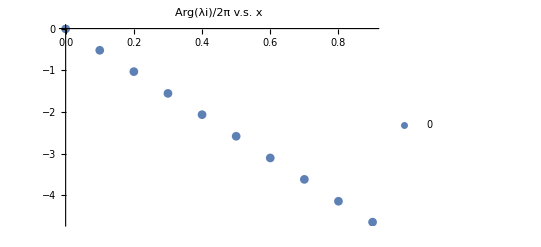

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/berry_laughlin_single_phase0","Table"];
n:=10
d=Table[i,{i,0,n-1,1}]/n;
ang1=Table[{d[[i]],codbar[[i]][[3]]/(2π)},{i,1,n}];
ang=Table[ang1[[i]],{i,1,n}];

ListPlot[ang1,PlotMarkers->Automatic,PlotLegends->{"0","1","2"},PlotLabel-> "Arg(λi)/2π v.s. x"]
```

```mathematica
codbar
```

{{0,0,0.0385805},{0,1,-3.04801},{0,2,-6.35117},{0,3,-9.9497},{0,4,-13.0751},{0,5,-16.1579},{0,6,-19.7317},{0,7,-22.7417},{0,8,-26.1441},{0,9,-29.1506},{1,0,-0.102628},{1,1,-3.28751},{1,2,-6.39084},{1,3,-9.80216},{1,4,-13.1936},{1,5,-16.3643},{1,6,-19.4403},{1,7,-22.2842},{1,8,-25.7804},{1,9,-28.9507},{2,0,0.143213},{2,1,-3.18136},{2,2,-6.60247},{2,3,-9.52641},{2,4,-12.8455},{2,5,-16.0096},{2,6,-19.4106},{2,7,-22.8788},{2,8,-25.6674},{2,9,-29.5294}}

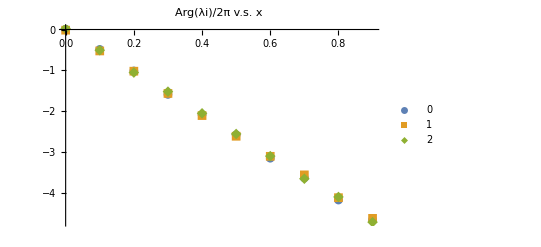

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/berry_laughlin_single_phase_set","Table"];
n:=10
d=Table[i,{i,0,n-1,1}]/n;
ang1=Table[{d[[i]],codbar[[i]][[3]]/(2π)},{i,1,n}];
ang2=Table[{d[[i]],codbar[[i+n]][[3]]/(2π)},{i,1,n}];
ang3=Table[{d[[i]],codbar[[i+2*n]][[3]]/(2π)},{i,1,n}];
ang=Table[{ang1[[i]], ang2[[i]],ang3[[i]]},{i,1,n}];

ListPlot[{ang1,ang2,ang3},PlotMarkers->Automatic,PlotLegends->{"0","1","2"},PlotLabel-> "Arg(λi)/2π v.s. x"]
```

```mathematica
ang1[[6]][[2]]
```

-2.57161